# Some Analysis for AG project

## Bimodal density population

```mathematica
mu1 = -4;
mu2 = 4;
sigma1 = 1;
sigma2 = 0.5;
```

```mathematica
f1 = 0.5;
```

```mathematica
(* Here we draw from a Bernouilli trial and then in Gaussian according to the result *)
```

```mathematica
data= Table[If[RandomReal[UniformDistribution[]] < f1, RandomReal[NormalDistribution[mu1, sigma1]], RandomReal[NormalDistribution[mu2, sigma2]]], {i, 1, 100000}];
```

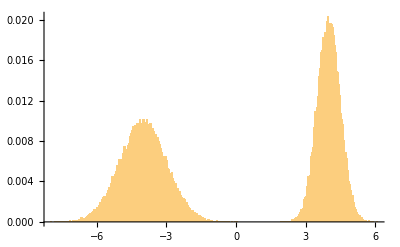

```mathematica
Histogram[data, 200, "Probability"]
```

### Tries to find functional form for posteriors on theta_v

```mathematica
f[x_, a_, b_] := x Exp[ -x/a + b]
```

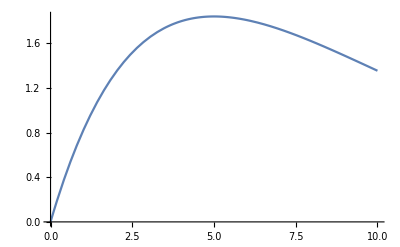

```mathematica
Plot[f[t, 5, 0], {t, 0, 10}]
```

```mathematica
Max[f[t, 5, 0], t]
```

Max[t,ⅇ^(-t/5) t]

```mathematica
Integrate[f[t, x, y], t]
```

-ⅇ^(-t/x+y) x (t+x)

```mathematica
Integrate[f[t, x, y], {t, 0, Infinity}]
```

ConditionalExpression[ⅇ^y x^2,Re[x]>0]

```mathematica
norm[x_, y_] = Integrate[f[t, x, y], {t, 0, Infinity}]
```

ConditionalExpression[ⅇ^y x^2,Re[x]>0]

```mathematica
F[x_, a_, b_] := f[x, a, b]/norm[a, b]
```

```mathematica
(* These would be the final shapes *)
```

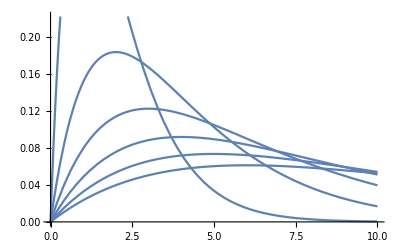

```mathematica
Plot[Table[F[x, i, 0], {i, 1, 6}], {x, 0, 10}]
```

### Functional form for epsilon_b varying with Gamma

```mathematica
(* Constraints are just that e_b is 0.1 at large gamma, and gamma/100 for small gamma *)
```

```mathematica
eb[a_] := Tanh[a/10.]/10.
```

```mathematica
Function[a,Tanh[a/10.]/10.]
```

Function[a,Tanh[a/10.]/10.]

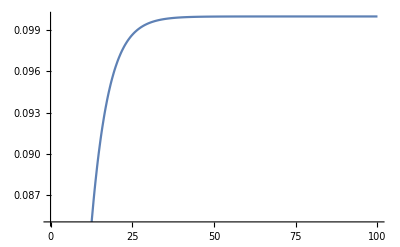

```mathematica
Plot[eb[t], {t, 0, 100}]
```

### Derivation for \bar{H} function of H in GW criterion

```mathematica
(* These are the antenna patterns (plus and cross) *)
Fp[x_, y_, z_] :=1/2 * Cos[2x] * (1 + Cos[y]^ 2) * Cos[2z] - Sin[2x]*Cos[y]*Sin[2z];
Fc[x_, y_, z_] :=1/2 * Sin[2x] *  (1 + Cos[y]^ 2) * Cos[2z] + Cos[2x]* Cos[y]* Sin[2z];
```

```mathematica
(*These are the averages of the antaenna patterns on position and ksi *)Integrate[Sin[theta] Fc[ksi, theta, phi] ^ 2, {ksi, 0, 2Pi}, {theta, 0, Pi}, {phi, 0, 2Pi}]/(2 * 2Pi * 2Pi)
```

1/5

```mathematica
Integrate[Sin[theta]Fp[ksi, theta, phi] ^ 2, {ksi, 0, 2Pi}, {theta, 0, Pi}, {phi, 0, 2Pi}]/(2 * 2Pi * 2Pi)
```

1/5

```mathematica
(* Theta square as function of all 4 angles *)
Theta2[i_, theta_, phi_, ksi_] := 4(Fp[ksi, theta, phi]^2(1 + Cos[i]^2)^2 + 4Fc[ksi, theta, phi] ^2 Cos[i] ^2);
```

```mathematica
NMaxValue[Theta2[i, theta, phi, ksi], {i, theta, phi, ksi}]
```

16.

```mathematica
(*Mean value on position and ksi*)Theta2i[i_] := Integrate[Sin[theta]Theta2[i, theta, phi, ksi] , {theta, 0, Pi}, {phi, 0, 2Pi}, {ksi, 0, 2Pi}]/(2* 2Pi * 2Pi)
```

```mathematica
NMaxValue[Theta2i[i], {i}]
```

6.4

```mathematica
Theta2i[i]
```

1/10 (35+28 Cos[2 i]+Cos[4 i])

```mathematica
(*Mean value on inclination. This basically defines the range*)
Theta = Integrate[Sin[i]Theta2i[i], {i, 0, Pi}]/2
```

64/25

```mathematica
N[Theta]
```

2.56

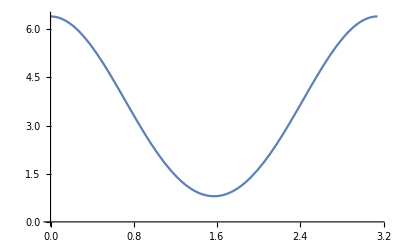

```mathematica
(*Plot of Theta2 after averaging on position and ksi*)
Plot[1/10 (35+28 Cos[2 i]+Cos[4 i]), {i, 0, Pi}]
```

```mathematica
Theta2i[0]
```

32/5

```mathematica
N[32/5]
```

6.4

```mathematica
(* Analytical form of Theta2 after averaging on position and ksi*)
Theta2if[i_]:= (1 + 6Cos[i]^2 + Cos[i]^4)/8
```

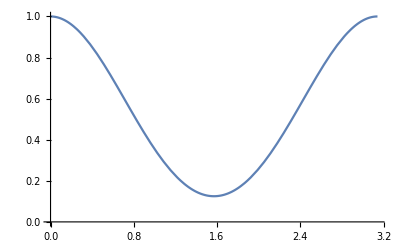

```mathematica
Plot[Theta2if[i], {i, 0, Pi}]
```

```mathematica
(*Nomrmalization constant for probability density in (x, theta)*)
norm = NIntegrate[Sin[i] * Theta2if[i]^(3/2), {i, 0, Pi/2}]/3
```

0.0968201

```mathematica
(*Probability density*)
p[x_, theta_] := Sin[theta] x^2 If[Theta2if[theta] > x ^2, 1, 0]/norm
```

```mathematica
(*Mean angle and standard deviation of GW-detected events*)
thetagw = NIntegrate[i p[x, i],{x, 0, 1}, {i, 0, Pi/2}];
stdgw = Sqrt[NIntegrate[(i - thetagw)^2p[x, i], {x, 0, 1}, {i, 0, Pi/2}]]
```

0.33841

```mathematica
thetagw * 180 /Pi
```

38.2295

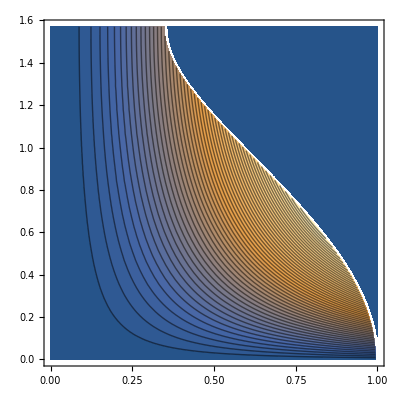

```mathematica
ContourPlot[p[x, y], {x, 0, 1}, {y, 0, Pi/2}, Contours->50]
```

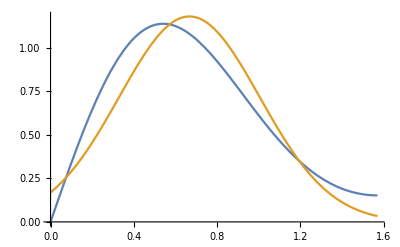

```mathematica
(*Marginal on theta of GW-detected events, and Gaussian approximation*)
Plot[{NIntegrate[p[x, theta], {x, 0, 1}], PDF[NormalDistribution[thetagw,stdgw], theta]}, {theta, 0, Pi/2}]
```

NIntegrate::nlim: theta = thetamax[0.0000204286] is not a valid limit of integration.

NIntegrate::nlim: theta = thetamax[0.0204286] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

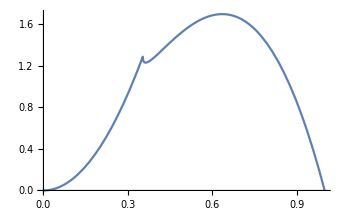

```mathematica
(* Marginal on x*)
Plot[{NIntegrate[p[x, theta], {theta, 0, Pi/2}, AccuracyGoal->Infinity, PrecisionGoal->10], NIntegrate[p[x, theta], {theta, 0, thetamax[x]}, AccuracyGoal->Infinity, PrecisionGoal->10]}, {x, 0, 1}]
```

```mathematica
(*Maximum angle for distance smaller than x*)
thetamax[x_] := If[x < 1/Sqrt[8], Pi/2, ArcCos[Sqrt[-3 + Sqrt[8 + 8x^2]]]]
```

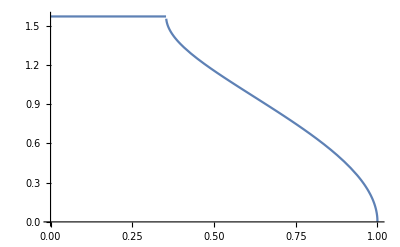

```mathematica
Plot[thetamax[x], {x, 0, 1}]
```

```mathematica
Series[thetamax[x], {x, 1, 3}]
```

(-1)^(1+Floor[(π-Arg[-1+x]-Arg[(1-√(-3+2 √2 √(1+x^2)))/(-1+x)])/(2 π)]) ⅈ^(1+2 Floor[Arg[(x-√(-3+2 √2 √(1+x^2)))/(-1+x)]/(2 π)]) (-√2 √(x-1)+(5 (x-1)^(3/2))/(12 √2)-(67 (x-1)^(5/2))/(320 √2)+O[x-1]^(7/2))

### Investigations on PM function of theta_v and d

```mathematica
(*some opening angle*)
thetaj=0.1
```

0.1

```mathematica
(*angular dependence of PM*)
f[theta_] := Sqrt[1 - Max[{theta, thetaj}]^2]Sin[theta]/(1 - Sqrt[1 - Max[{theta, thetaj}]^2] Cos[theta]);
(*GW criterion*)
g[theta_] := Sqrt[(1 + 6Cos[theta]^2 + Cos[theta]^4)/8]
```

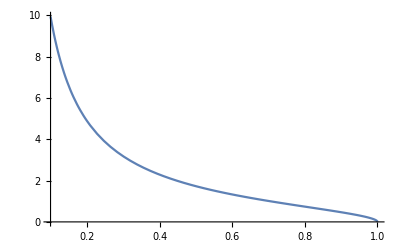

```mathematica
Plot[f[t], {t, 0.1, 1}]
```

```mathematica
PM[theta_, d_] := f[theta]/d
```

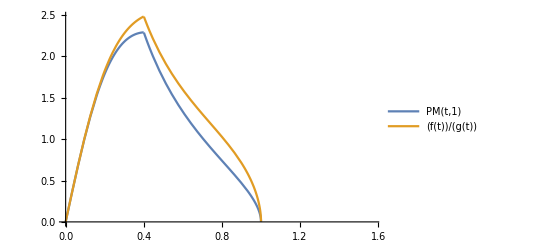

```mathematica
(*Lower limits on PM(theta) with and withour GW criterion*)
Plot[{PM[ t, 1], f[t]/g[t]},{t, 0, Pi/2}, PlotLegends->"Expressions"]
```

```mathematica
(*Maximum angle to GW detect function of distance*)
thetaM[D_]:=ArcCos[Sqrt[-3 + Sqrt[8]Sqrt[1 + D^2]]]
```

```mathematica
Dj=g[thetaj]
```

0.92262

Max::nord: Invalid comparison with 1.5708-0.4032 ⅈ attempted.

Max::nord: Invalid comparison with 1.5708-0.402541 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 1.5708-0.4032 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

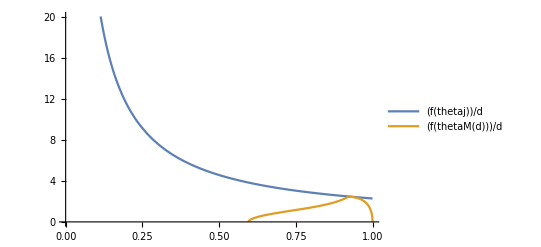

```mathematica
(*Upper limits on PM(D)*)
Plot[{f[thetaj]/d, f[thetaM[d]]/d}, {d, 0, 1}, PlotLegends->"Expressions"]
```

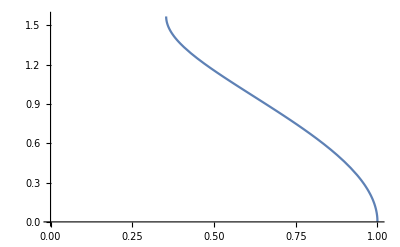

```mathematica
Plot[thetaM[d], {d, 0, 1}]
```

### Asymmetrical normal distribution

```mathematica
(*PDF*)
pdf[mu_, sig1_, sig2_, x_] = 2/(Sqrt[2Pi](sig1 + sig2))If[x <mu, Exp[-(x - mu)^2/(2sig1^2)], Exp[-(x-mu)^2/(2sig2^2)]]
```

(√(2/π) If[x<mu,Exp[-(x-mu)^2/(2 sig1^2)],Exp[-(x-mu)^2/(2 sig2^2)]])/(sig1+sig2)

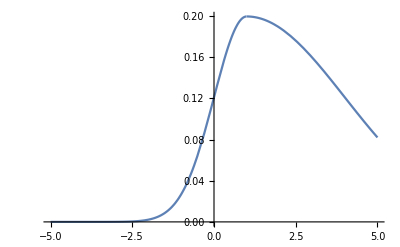

```mathematica
Plot[pdf[1, 1, 3, x], {x, -5, 5}]
```

```mathematica
(*CDF*)
cdf [mu_, sig1_,sig2_, x_] := Sqrt[2]If[x < mu, Sqrt[2Pi]sig1 CDF[NormalDistribution[mu, sig1], x], Sqrt[2Pi](sig1 - sig2)/2 + Sqrt[2Pi]sig2 CDF[NormalDistribution[mu, sig2], x]]/((sig1 + sig2)Sqrt[Pi])
```

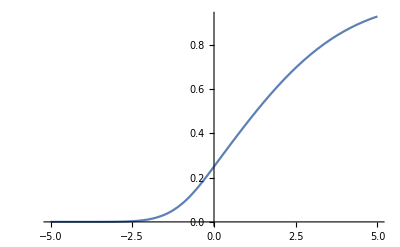

```mathematica
Plot[cdf[0, 1, 3, x], {x, -5, 5}]
```

```mathematica
(*Probability of being left of mu*)
cdf[mu, sig1, sig2, mu]//Simplify
```

sig1/(sig1+sig2)

### Fractions of joint detections

```mathematica
p[mu_, sig_,m_,n_] := PDF[LogNormalDistribution[mu, sig],n]n^(-m)
```

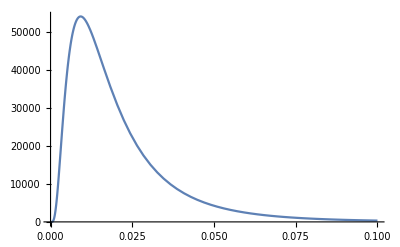

```mathematica
Plot[p[-3, 0.75, 2, x], {x, 0,0.1}]
```

```mathematica
Assuming[sig > 0, Integrate[p[mu, sig, m, n], {n, 0, Infinity}]]
```

ⅇ^(1/2 m (-2 mu+m sig^2))

```mathematica
(* Fraction of joint dtected events, for a flux tau (tau = En^4/5...eb^4/5/(D^2s))*)frac[tau_] := 3NIntegrate[x^2 Sin[theta]If[Sqrt[(1 + 6Cos[theta]^2 + Cos[theta]^4)/8] > x, 1, 0] If[tau Max[{theta, thetaj}]^(-4.3)> x^2, 1, 0], {x, 0, 1}, {theta, 0, Pi/2}, MaxRecursion->20] //N
```

```mathematica
frac[1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0968494 and 0.0000203629 for the integral and error estimates.

0.290548

```mathematica
lfrac[tau_]:= Log10[frac[tau]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.3929×10^-7 and 5.77614×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000139089 and 1.85521×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000439074 and 5.73194×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

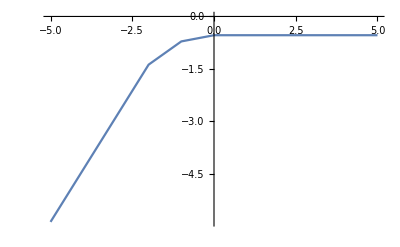

```mathematica
(* Fraction is found to be a power law then a constant*)
ListLinePlot[Table[{i, lfrac[10^i]},{i, -7, 5}]]
```

```mathematica
(* The slope for tau < 1.e-3 is 3/2*)
LinearModelFit[Table[{i, lfrac[10^i]},{i, -5, -2}], x, x]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.3929×10^-7 and 5.77614×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000139089 and 1.85521×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000439074 and 5.73194×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

FittedModel[1.62057+1.50013 x]

```mathematica
0.4^4.3/8
```

0.0024309

### Fraction function of lognormal center density

```mathematica
(* This is a good approximation of the fraction as function of n0*)
ifrac[x_] := 29/(1 + Exp[-(x + 0.5)])
```

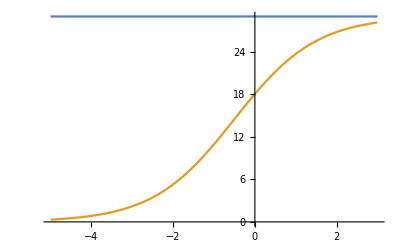

```mathematica
Plot[{29,ifrac[x]}, {x, -5, 3}]
```

```mathematica
(* Fraction of low density after observational selection *)
ptilde[p_, n1_, n2_] :=frac[n1] (1- p)/(frac[n1](1 - p) + frac[n2]p)
```

```mathematica
norm[n1_, n2_, Nt_, M_] :=NIntegrate[ptilde[p, n1, n2]^M (1 - ptilde[p, n1, n2])^(Nt -M), {p, 0, 1}]//N
```

SetDelayed::write: Tag Real in 0.0968201[n1_,n2_,Nt_,M_] is Protected.

$Failed

```mathematica
norm[-5, 1, 10, 5]
```

0.0968201[-5,1,10,5]

```mathematica
(* Posterior on p2 (intrinsic number of high density mergers) after seeing M low density out of N total mergers *)
posterior[p2_, n1_, n2_, N_, M_] := ptilde[p2, n1, n2]^M (1 - ptilde[p2, n1, n2])^(N - M)/norm[n1, n2, N, M]
```

```mathematica
Plot[{posterior[p2, -3, 0, 5, 5], posterior[p2, -3, 0, 8, 8], posterior[p2, -3, 0, 10, 10], posterior[p2, -3, 0, 20, 20]}, {p2, 0, 1}, PlotLegends->{"5/5", "8/8", "10/10", "20/20"}, AxesLabel->{HoldForm[p_ 2],HoldForm[posterior on p2]}, PlotRange->{0, 0.5}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(* Fraction of observed high-density function of instrinsic p2 and density n2 of high density events *)
ofrac2[p2_, n2_]:= p2 ifrac[n2]/((1 - p2)ifrac[-3] + p2 ifrac[n2])
```

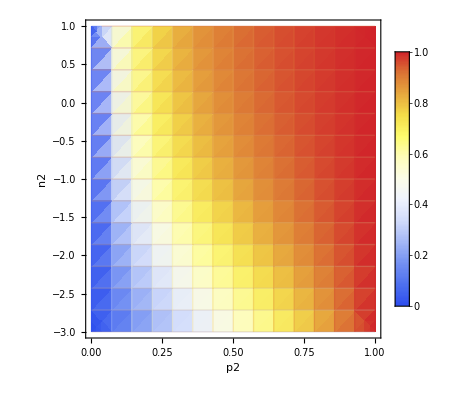

```mathematica
DensityPlot[ofrac2[p2, n2], {p2, 0,1}, {n2, -3, 1},FrameLabel->{{HoldForm[n2],None},{HoldForm[p2],None}}, PlotLegends->Automatic, Mesh->Full, ColorFunction->"TemperatureMap"]
```

### Relative contributions of Blue and Red kilonova

```mathematica
(* Integration limits on theta and phi according to FD notes *)
thetaminc[tv_, tk_] := Max[0, tv-tk];thetamaxc[tv_, tk_] := tv + tk;thetamincc[tv_, tk_] := Pi - thetamaxc[tv, tk];thetamaxcc[tv_, tk_] := Pi - thetaminc[tv, tk];phiminc[tv_, tk_,t_] := If[And[t<tk - tv && tv<tk], 0, ArcCos[(Cos[tv]Cos[t]-Cos[tk])/(Sin[tv]Sin[t])]] ;phimaxc[tv_, tk_, t_] := 2Pi - phiminc[tv, tk, t];phimincc[tv_, tk_,t_] := If[And[t > Pi - (tk-tv)&& tv<tk], 0, ArcCos[(Cos[tv]Cos[t]+Cos[tk])/(Sin[tv]Sin[t])]];phimaxcc[tv_, tk_, t_] := 2Pi - phimincc[tv, tk, t]
```

```mathematica
(*Integral giving the contribution of the blue kilonova (in spherical cap) as function of viewing angle tv and spherical cap angle tk *)
f[tv_, tk_] := NIntegrate[Cos[t]Sin[t],{t, Min[Pi/2,thetaminc[tv, tk]], Min[Pi/2,thetamaxc[tv, tk]]} ,{phi,phiminc[tv,tk,t], phimaxc[tv, tk, t]}] +NIntegrate[Cos[t]Sin[t],{t, Min[Pi/2,thetamincc[tv, tk]], Min[Pi/2,thetamaxcc[tv, tk]]},{phi,0, phimincc[tv,tk,t]}] + NIntegrate[Cos[t]Sin[t],{t, Min[Pi/2,thetamincc[tv, tk]], Min[Pi/2,thetamaxcc[tv, tk]]},{phi,phimaxcc[tv,tk,t], 2Pi}]
```

```mathematica
f[Pi/2, Pi/4]
```

0.570796

```mathematica
(* Same but analytic*)
g[tv_, tk_] := Integrate[Cos[t]Sin[t],{t, Min[Pi/2,thetaminc[tv, tk]], Min[Pi/2,thetamaxc[tv, tk]]} ,{phi,phiminc[tv,tk,t], phimaxc[tv, tk, t]}] +Integrate[Cos[t]Sin[t],{t, Min[Pi/2,thetamincc[tv, tk]], Min[Pi/2,thetamaxcc[tv, tk]]},{phi,0, phimincc[tv,tk,t]}] + Integrate[Cos[t]Sin[t],{t, Min[Pi/2,thetamincc[tv, tk]], Min[Pi/2,thetamaxcc[tv, tk]]},{phi,phimaxcc[tv,tk,t], 2Pi}]
```

```mathematica
g[tv, tk]//Simplify
```

2 ∫_Min[π/2,π-tk-tv]^Min[π/2,π-Max[0,-tk+tv]] Cos[t] If[t+tk>π+tv&&tv<tk,0,ArcCos[(Cos[tv] Cos[t]+Cos[tk])/(Sin[tv] Sin[t])]] Sin[t]ⅆt+∫_Min[π/2,Max[0,-tk+tv]]^Min[π/2,tk+tv] (π-If[t+tv<tk&&tv<tk,0,ArcCos[(Cos[tv] Cos[t]-Cos[tk])/(Sin[tv] Sin[t])]]) Sin[2 t]ⅆt

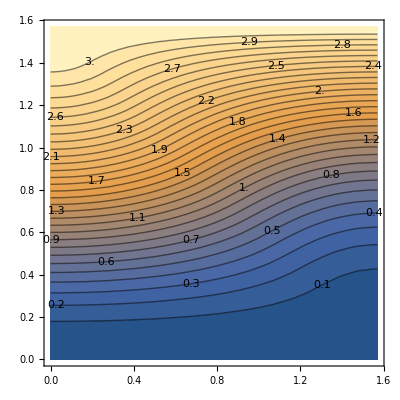

```mathematica
ContourPlot[f[tv, tk], {tv, 0, Pi/2}, {tk, 0, Pi/2}, Contours->30, ContourLabels->True]
```

```mathematica
(*Ratio of blue to red*)
eta[tv_, tk_] := f[tv, tk]/(Pi - f[tv, tk])
```

```mathematica
(*Ratio of Blue/Red contributions as function of viewing angle for different cap angles *)
Plot[{eta[tv, Pi/3], eta[tv, Pi/4], eta[tv, Pi/6], eta[tv, Pi/8], eta[tv, Pi/10]},{tv, 0, Pi/2}, PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
output = OpenWrite["/Users/duque/f005.data"]
```

OutputStream[…]

```mathematica
For[i = 0, i < 100, i++, WriteLine[output, Table[f[j*Pi/200, i*Pi/200], {j, 0, 99}]]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
For[i = 0, i < 100, i++,
WriteLine[output, {i * Pi/200, f[i*Pi/200, 0.05]}]]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Close[output]
```

/Users/duque/f005.data

```mathematica
F[x_] := NIntegrate[Exp[t]t^(-0.65), {t, 0, x}]
```

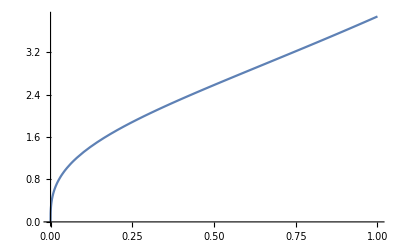

```mathematica
Plot[F[a], {a, 0, 1}]
```

```mathematica
Series[F[a], {a, 0, 3}]
```

NIntegrate::nlim: t = a is not a valid limit of integration.

NIntegrate::nlim: t = (a+0.)+O[a+0.]^5 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Power::infy: Infinite expression 1/0^0.65 encountered.

Power::infy: Infinite expression 1/0^1.65 encountered.

Power::infy: Infinite expression 1/0^0.65 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ComplexInfinity a+Indeterminate a^2+Indeterminate a^3+O[a]^4

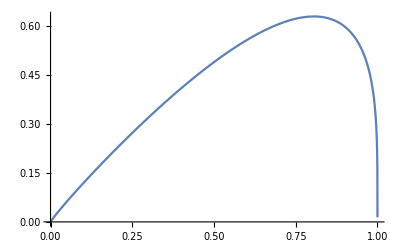

```mathematica
Plot[x^(3/4)((1 - x^2)x^(2 - 1.3))^0.25, {x, 0, 1}]
```

```mathematica
Maximize[{x^(3/4)((1 - x^2)x^(2 - 1.3))^0.25, x<1 && x> 0},x ]
```

{0.630217,{x→0.805682}}

```mathematica
Hypergeometric1F1[1-1.3/2, 2-1.3/2, 0.42]
```

1.12343

```mathematica
1 + (1 - 1.3/2)*0.42/(2 - 1.3/2)
```

1.10889

```mathematica
Derivative[0, 0, 1][Hypergeometric1F1][a, b, z]
```

(a Hypergeometric1F1[1+a,1+b,z])/b

```mathematica
F[tau_, a_] := Exp[-tau]tau^(5/8 - a/4) Hypergeometric1F1[1-a, 2-a,tau]^(1/4)
```

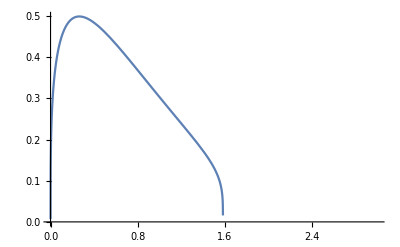

```mathematica
Plot[F[tau, 1.3], {tau, 0, 3}]
```

```mathematica
Series[F[tau, a], {tau, 0, 3}]
```

tau^(-a/4) ((-tau)^a tau^-a (tau^a (-((-1+a) Gamma[1-a])/tau+O[tau]^7)+tau^a (((-1+a) Gamma[1-a,0])/tau+O[tau]^7)+ⅇ^(2 ⅈ (1-a) π Floor[-Arg[tau]/(2 π)]) ((-1)^-a+((-1)^-a (-1+a) tau)/(-2+a)+((-1)^-a (-1+a) tau^2)/(2 (-3+a))+((-1)^-a (-1+a) tau^3)/(6 (-4+a))+((-1)^-a (-1+a) tau^4)/(24 (-5+a))+((-1)^-a (-1+a) tau^5)/(120 (-6+a))+O[tau]^6)))^(1/4) (tau^(5/8)-tau^(13/8)+tau^(21/8)/2+O[tau]^(25/8))

```mathematica
Assuming[0<a && a < 1&& tau > 0, Series[F[tau, a], {tau, 0, 3}]]
```

tau^(-a/4) ((-tau)^a tau^-a (((-1)^-a tau)/(1-a)+((-1)^-a tau^2)/(2-a)-((-1)^-a tau^3)/(2 (-3+a))-((-1)^-a tau^4)/(6 (-4+a))-((-1)^-a tau^5)/(24 (-5+a))+O[tau]^6))^(1/4) (((1-a)/tau)^(1/4) tau^(5/8)-((1-a)/tau)^(1/4) tau^(13/8)+1/2 ((1-a)/tau)^(1/4) tau^(21/8)+O[tau]^(25/8))

```mathematica
Derivative[1, 0][F][tau, a]
```

(5/8-a/4) ⅇ^-tau tau^(-3/8-a/4) (((-1+a) (-tau)^a Gamma[1-a,0,-tau])/tau)^(1/4)-ⅇ^-tau tau^(5/8-a/4) (((-1+a) (-tau)^a Gamma[1-a,0,-tau])/tau)^(1/4)+(ⅇ^-tau tau^(5/8-a/4) (-((-1+a) ⅇ^tau)/tau-((-1+a) (-tau)^a Gamma[1-a,0,-tau])/tau^2-((-1+a) a (-tau)^(-1+a) Gamma[1-a,0,-tau])/tau))/(4 (((-1+a) (-tau)^a Gamma[1-a,0,-tau])/tau)^(3/4))

```mathematica
FullSimplify[%27]
```

-(x-1)-7/4 (x-1)^2+O[x-1]^3